# xJüs - Flexible Hexapod

## Target Angle Generation via Fourier Estimation

## Desired trajectory definition

```mathematica
ClearAll["Global`*"];
```

#### Estimation parameter

```mathematica
M=10;  (* Number of Fourier terms to use *)
```

#### Calculate basic parameters

```mathematica
Tg=T*dc; (* Time per period on the ground *)
Ta=T*(1-dc); (* Time per period in the air *)
ωg=θg/Tg; (* Angular velocity of the ground movement *)
θa=2π-θg; (* Air contact angle range *)
ωa=θa/Ta; (*Angular velocity of the air movement *)
```

#### Define the piecewise linear velocity profile

```mathematica
θdotpiecewise=Simplify[Piecewise[{{ωg,Mod[t,T]<Tg},{ωa,Tg≤Mod[t,T]<T}}]]
```

Piecewise[{{θg/(dc T), Mod[t,T]<dc T}, {(-2 π+θg)/((-1+dc) T), dc T≤Mod[t,T]<T}, {0, True}}]

```mathematica
f=FourierSeries[θdotpiecewise,t,5,FourierParameters->{1,2π/T},Assumptions->{T>0,0.<dc<1.,0.<θg<2π}]
```

(2 π)/T-(ⅈ ⅇ^(-2 ⅈ dc π+(2 ⅈ π t)/T) (-1+ⅇ^(2 ⅈ dc π)) (2 dc π-θg))/(2 (-1+dc) dc π T)-(ⅈ ⅇ^(-(2 ⅈ π t)/T) (-1+ⅇ^(2 ⅈ dc π)) (2 dc π-θg))/(2 (-1+dc) dc π T)-(ⅈ ⅇ^(-4 ⅈ dc π+(4 ⅈ π t)/T) (-1+ⅇ^(4 ⅈ dc π)) (2 dc π-θg))/(4 (-1+dc) dc π T)-(ⅈ ⅇ^(-(4 ⅈ π t)/T) (-1+ⅇ^(4 ⅈ dc π)) (2 dc π-θg))/(4 (-1+dc) dc π T)-(ⅈ ⅇ^(-6 ⅈ dc π+(6 ⅈ π t)/T) (-1+ⅇ^(6 ⅈ dc π)) (2 dc π-θg))/(6 (-1+dc) dc π T)-(ⅈ ⅇ^(-(6 ⅈ π t)/T) (-1+ⅇ^(6 ⅈ dc π)) (2 dc π-θg))/(6 (-1+dc) dc π T)-(ⅈ ⅇ^(-8 ⅈ dc π+(8 ⅈ π t)/T) (-1+ⅇ^(8 ⅈ dc π)) (2 dc π-θg))/(8 (-1+dc) dc π T)-(ⅈ ⅇ^(-(8 ⅈ π t)/T) (-1+ⅇ^(8 ⅈ dc π)) (2 dc π-θg))/(8 (-1+dc) dc π T)-(ⅈ ⅇ^(-10 ⅈ dc π+(10 ⅈ π t)/T) (-1+ⅇ^(10 ⅈ dc π)) (2 dc π-θg))/(10 (-1+dc) dc π T)-(ⅈ ⅇ^(-(10 ⅈ π t)/T) (-1+ⅇ^(10 ⅈ dc π)) (2 dc π-θg))/(10 (-1+dc) dc π T)

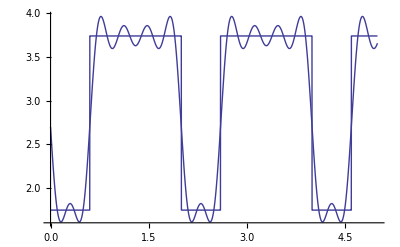

```mathematica
Plot[{f,θdotpiecewise}/.{T->2,θg->π/3,dc->0.3},{t,0,5}]
```

## Estimation with Fourier Sine Series

#### Estimate with a fourier series

```mathematica
A[n_]=FourierCoefficient[θdotpiecewise,t,n,FourierParameters->{1,(2π)/T},Assumptions->{T>0,0.<dc<1.,0.<θg<2π}]
```

FourierCoefficient[Piecewise[{{θg/(dc T), Mod[t,T]<dc T}, {(-2 π+θg)/((-1+dc) T), dc T≤Mod[t,T]<T}, {0, True}}],t,n,FourierParameters→{1,(2 π)/T},Assumptions→{T>0,0.<dc<1.,0.<θg<2 π}]

```mathematica
Table[A[n],{n,1,5}]
```

{-(ⅈ ⅇ^(-2 ⅈ dc π) (-1+ⅇ^(2 ⅈ dc π)) (2 dc π-θg))/(2 (-1+dc) dc π T),-(ⅈ ⅇ^(-4 ⅈ dc π) (-1+ⅇ^(4 ⅈ dc π)) (2 dc π-θg))/(4 (-1+dc) dc π T),-(ⅈ ⅇ^(-6 ⅈ dc π) (-1+ⅇ^(6 ⅈ dc π)) (2 dc π-θg))/(6 (-1+dc) dc π T),-(ⅈ ⅇ^(-8 ⅈ dc π) (-1+ⅇ^(8 ⅈ dc π)) (2 dc π-θg))/(8 (-1+dc) dc π T),-(ⅈ ⅇ^(-10 ⅈ dc π) (-1+ⅇ^(10 ⅈ dc π)) (2 dc π-θg))/(10 (-1+dc) dc π T)}

#### Estimate with a fourier sine series

Constant to make the piecewise function odd, so we can do only sine series:

```mathematica
A0=Simplify[(ωa+ωg)/2]
```

2.61799

Sin coefficients of the odd function:

```mathematica
B[n_]=FourierSinCoefficient[θdotpiecewise-A0,t,n,FourierParameters->{1,(2π)/T},Assumptions->{T>0,0.5<dc<1.0}]
```

-((-1+(-1)^n) (2 dc π-θg))/((-1+dc) dc n π T)

We can see that every other coefficient is zero, so substitute n=2m-1 to get new coefficients:

```mathematica
(* B[m_]=Simplify[B[2m-1],Assumptions->m∈Integers] *)
```

Now plug this into the series to get θ_d'(t):

```mathematica
θdot[t_]=A0+∑_(m=1)^M B[m]Sin[(2π(2m-1))/T t];
```

Integrate to get θ_d(t), with a constant such that θ_d(0)=0:

```mathematica
θ[t_]=Integrate[θdot[t],t];
θ[t_]=θ[t]-θ[0];
```

## Plotting Specific Values of Design Parameters

```mathematica
Clear[dc,T,θg]
```

```mathematica
dc=0.3;
T=2; (* Overall period *)
θg=π/4; (* Ground contact angle range *)
```

```mathematica
Plot[180/π*θ[t],{t,0,T},AxesLabel->{"t (s)",""},PlotLabel->"θ_d(t), T = 1s"];
```

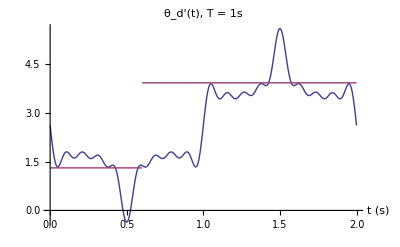

```mathematica
Plot[{θ'[t],θdotpiecewise},{t,0,T},AxesLabel->{"t (s)",""},PlotLabel->"θ_d'(t), T = 1s"]
```

```mathematica
(*Plot[θ''[t],{t,0,2T},PlotRange->All]*)
```

## Printing Trajectory to a File

#### Parameters

```mathematica
Δt=50; (* milliseconds *) 
startTime=Δt/2000.;
length=4T;
gearRatio = 729/25;
angleToQC=((512*4)/(2π))*gearRatio;
angVelToRPM=(60/(2π))*gearRatio;
```

#### Generate Vectors

```mathematica
tPoints=Range[startTime,startTime+length,Δt/1000];
```

```mathematica
tPoints=Append[tPoints,startTime+length];
```

```mathematica
positions=Round[θ[tPoints]*angleToQC];
```

```mathematica
velocities=Round[θ'[tPoints]*angVelToRPM];
```

```mathematica
timeIntervals=ConstantArray[Δt,Length[tPoints]];
```

Append last point, signal to stop.

```mathematica
positions=Append[positions,positions[[-1]]];
velocities=Append[velocities,0];
timeIntervals=Append[timeIntervals,0];
```

```mathematica
trajectoryLeft={positions,velocities,timeIntervals}ᵀ;
trajectoryRight={-positions,-velocities,timeIntervals}ᵀ;
```

#### Write to file

```mathematica
saveFile[trajectory_,name_]:=(
file=FileNameJoin[{NotebookDirectory[],name}];
str=ExportString[trajectory,"CSV","TableHeadings"->{"qc","rpm","ms"}];
str=StringReplace[str,","->";"];
str=StringReplace[str,"\n"->";\n"];
str=StringJoin[str,";"];
Export[file,str];
)
```

```mathematica
saveFile[trajectoryLeft,"leftLeg.csv"];
saveFile[trajectoryRight,"rightLeg.csv"];
```